```mathematica
h=73/10; r2=73/10; r1=2;
```

```mathematica
Ω=RegionDifference[Rectangle[{0,0},{r2,h}],Disk[{0,0},2]];
```

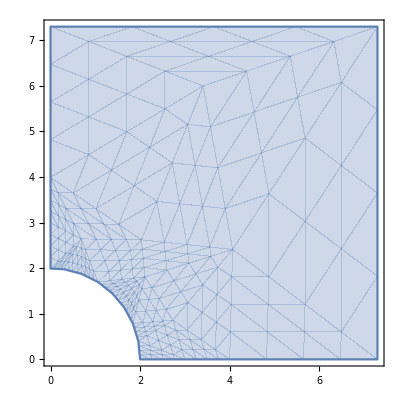

```mathematica
RegionPlot[Ω]
```

```mathematica
<<NDSolve`FEM`
```

```mathematica
mesh=FEM`ToElementMesh[Ω]
```

FEM`ToElementMesh[BooleanRegion[#1&&!#2&,{Rectangle[{0,0},{73/10,73/10}],Disk[{0,0},2]}]]

```mathematica
lpc=D[ϕ[r,z],z,z]+D[ϕ[r,z],r,r]+1/r D[ϕ[r,z],r]
```

ϕ^(0,2)[r,z]+(ϕ^(1,0)[r,z])/r+ϕ^(2,0)[r,z]

```mathematica
solc=NDSolveValue[
{lpc==NeumannValue[0,r==0&&r1<z<h]+NeumannValue[0,z==0&&r1<r<r2],
DirichletCondition[ϕ[r,z]==-1,r^2+z^2==r1^2],
ϕ[r,h]==0,ϕ[r2,z]==0},ϕ,{r,z}∈Ω
]
```

InterpolatingFunction[…]

```mathematica
solc["ElementMesh"]
```

NDSolve`FEM`ElementMesh[{{0.,7.3},{0.,7.3}},{NDSolve`FEM`TriangleElement[<596>]}]

```mathematica
solca=NDSolveValue[
{lpc==NeumannValue[0,r==0&&r1<z<h]+NeumannValue[0,z==0&&r1<r<r2],
DirichletCondition[ϕ[r,z]==-1,r^2+z^2==r1^2],
ϕ[r,h]==0,ϕ[r2,z]==0},ϕ,{r,z}∈Ω,AccuracyGoal->30,PrecisionGoal->30
]
```

InterpolatingFunction[{{0., 7.3}, {0., 7.3}}, <>]

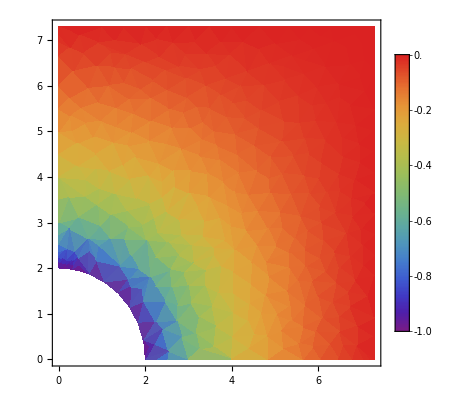

```mathematica
DensityPlot[solc[r,z],{r,z}∈Ω,Mesh->None,ColorFunction->"Rainbow",PlotRange->All,PlotLegends->Automatic]
```

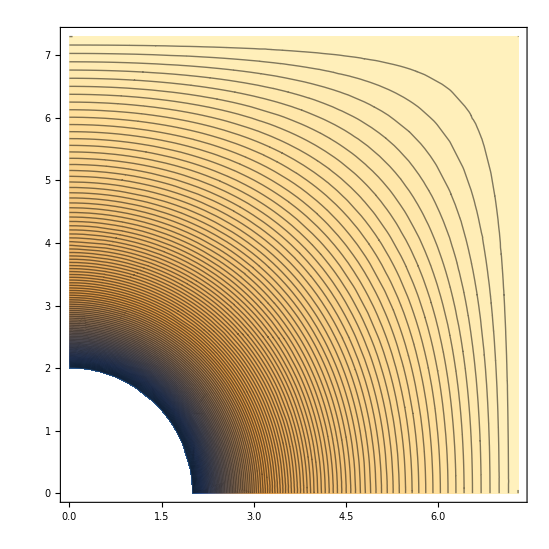

```mathematica
ContourPlot[solc[r,z],{r,z}∈Ω,Contours->Range[-1,0,.01]]
```

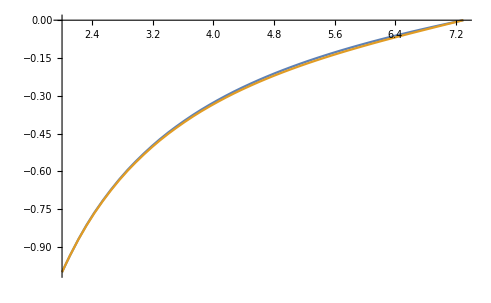

```mathematica
Plot[{solc[x,0],solc[0,x]},{x,2,h}]
```

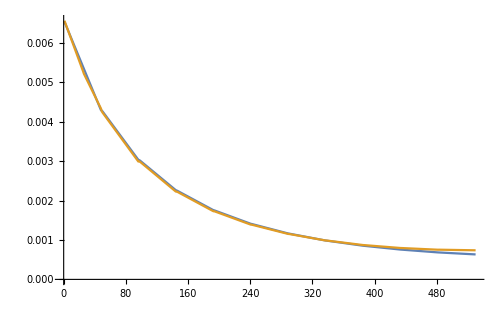

```mathematica
ListPlot[{Differences[solc[#,0]&/@Range[2,7.3,.01]],Differences[solc[0,#]&/@Range[2,7.3,.01]]},Joined->True]
```

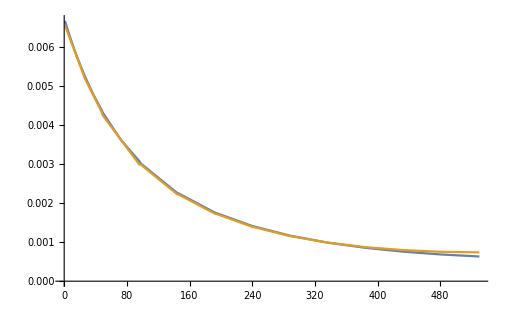

```mathematica
ListPlot[{Differences[solca[#,0]&/@Range[2,7.3,.01]],Differences[solc[0,#]&/@Range[2,7.3,.01]]},Joined->True]
```